# Historical “Data” for Backtesting

## This is part 1 of 2 of the supplemental material for Sec. 11.

Instructions: Simulate price histories and write them to storage before running the C program.

## Directory

```mathematica
exportDirectory=NotebookDirectory[]<>"output/priceHistory";
```

```mathematica
SetDirectory@exportDirectory
```

## Simulate Price Histories

### Simulate a geometric mean-reverting process

While Wolfram has a GeometricBrownianMotion[], it does not have a GeometricOrnsteinUhlenbeck[]. I will program my own using the more general ItoProcess[].

The Ornstein-Uhlenbeck model in log-price, x≡ln(S/S_0), is (see Sec. 10.1 of the paper)
	dx(t)= σ Z(t) √dt-θ • (x-m)dt ,
where σ is the volatility, m is the asymptotic mean, and θ is the mean-reversion speed. 
The relation between dx(t) and dS(t) is
	(dS(t))/(S(t))=dx(t)+σ^2/2 dt .
Therefore, the geometric Ornstein-Uhlenbeck process is 
	dS(t)= [-θ • (ln(S/S_0)-m)+σ^2/2]S(t)dt+σ S(t)dB(t) .

#### Simulation parameters

```mathematica
σ=1;m=0.31;θ=0.26;
```

```mathematica
S0=1;T=1;dt=0.01;𝒩=T/dt
```

100.

```mathematica
{m,σ^2/(2θ),m+σ^2/(2θ),S0 Exp[m+σ^2/(2θ)],Exp[σ^2/(2θ)]} (* An aside for Sec. 11.2.2 *)
```

{0.31,1.92308,2.23308,9.32853,6.84198}

I will define an interface in the style of OrnsteinUhlenbeckProcess[]:

```mathematica
GeometricOrnsteinUhlenbeckProcess[m_,σ_,θ_,S0_]:=ItoProcess[
{(-θ(Log[S[t]/S0]-m)+σ^2/2)S[t],σ S[t]},{S,S0},{t,0}
]
```

#### Simulate a collection of histories

```mathematica
numberOfPaths=5;
```

```mathematica
priceHistory=RandomFunction[
GeometricOrnsteinUhlenbeckProcess[m,σ,θ,S0],{0,T,dt},
numberOfPaths]
```

TemporalData[…]

## Plot the Results

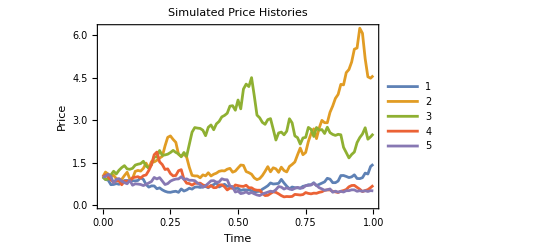

```mathematica
priceHistoryPlot=ListLinePlot[priceHistory,
PlotRange->All,
PlotLegends->Range@numberOfPaths,
PlotLabel->Style["Simulated Price Histories",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["Price",FontSize->12]},
FrameStyle->Directive[Black,12]
]
```

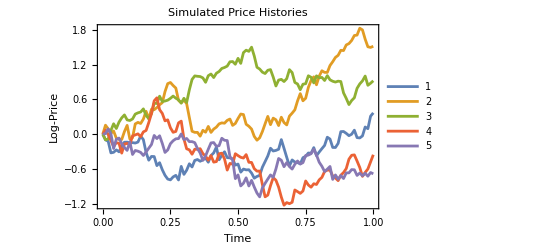

```mathematica
logPriceHistoryPlot=ListLinePlot[Log@priceHistory,(* Log threads over lists *)
PlotRange->All,
PlotLegends->Range@numberOfPaths,
PlotLabel->Style["Simulated Price Histories",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["Log-Price",FontSize->12]},
FrameStyle->Directive[Black,12]
]
```

### Write Plots and Parameters to Storage

```mathematica
Export["priceHistoryPlot.pdf",priceHistoryPlot]
```

priceHistoryPlot.pdf

```mathematica
Export["logPriceHistoryPlot.pdf",logPriceHistoryPlot]
```

logPriceHistoryPlot.pdf

```mathematica
Export["simulationParameters.txt",{
"*********************",
"Simulation parameters",
"*********************",
" ",
"Temporal increment (dt): "<>ToString@dt,
"Total time (T): "<>ToString@T,
"Volatility (σ): "<>ToString@σ,
"Asymptotic mean (m): "<>ToString@m,
"Mean-reversion speed (θ): "<>ToString@θ
}]
```

simulationParameters.txt

### Write the Price Histories as a CSV

```mathematica
priceHistory["Properties"]
```

{Components,DateList,DatePath,DatePaths,Dates,FirstDates,FirstTimes,FirstValues,LastDates,LastTimes,LastValues,Part,Path,PathComponent,PathComponents,PathCount,PathDates,PathFunction,PathFunctions,PathLength,PathLengths,Paths,PathTimes,SliceData,SliceDistribution,TimeList,Times,ValueDimensions,ValueList,Values}

```mathematica
Table[
Export["priceHistory"<>ToString@n<>".csv",
SetPrecision[{priceHistory["ValueList"][[n]]},4]
],
{n,1,numberOfPaths}
](* I need to wrap that in a list so that it will produce a row instead of a column *)
```

{priceHistory1.csv,priceHistory2.csv,priceHistory3.csv,priceHistory4.csv,priceHistory5.csv}

```mathematica
Export["dates.csv",SetPrecision[{priceHistory["Times"]},4]]
```

dates.csv